## Exponential approximations derivations for stars and gas

By Davi Rodrigues & Alejandro Hernandez-Arboleda
This file is part of the NAVanalysis code
July, 2022

```mathematica
pathBaseDirectory = NotebookDirectory[];
pathOutputDirectory = FileNameJoin[{pathBaseDirectory, "Output"}];
pathAuxDirectory = FileNameJoin[{pathBaseDirectory, "AuxiliaryData"}];

SetDirectory @ NotebookDirectory[];
Needs @ "NAVbaseCode`";
Get @ "NAVauxiliaryFunctions.wl";

SetDirectory @ pathOutputDirectory;
```

## General definitions

```mathematica
Clear[chi2];

(*
  vExp comes from Binney & Tremaine 2nd Ed., eq.(2.165). 
  It is assumed that  Σ = Subscript[Σ, 0] ⅇ^(-R/h), where Subscript[Σ, 0] has dimension of mass/length^2, it  is the surface mass density.
*)

vExp[R_,logSigma0_,h_]= Block[{y}, 
  y = R/(2 h);
  kpc Sqrt[4 π G0 10^logSigma0 h y^2 (BesselI[0,y] BesselK[0,y] - BesselI[1,y] BesselK[1,y])]
];

chi2[model_List, dataObs_List, uncertainty_List] := chi2[model, dataObs, uncertainty]  = Total[(model-dataObs)^2/uncertainty^2];
```

## Stellar contribution

```mathematica
Clear[fitExpVdisk, fitExpVdiskPlot, associationFitExpVdisk];

associationFitExpVdisk::usage="associationFitExpVdisk[galaxyNumber, data(R x Vdisk)] fits the radial vs disk velocity curve data as a rotation curve for an exponential disk and returns an association with several data. "<>
  "For fitting, it is assumed an uncertainty of either 10% on the velocity or at least 2 km/s. The important point is not the porportionality constant, but that the uncertainty is proportional to the velocity."<>
  "If data = {},  associationFitExpVdisk returns {}.";

associationFitExpVdisk[galaxyNumber_, dataRVdisk_List] := fitExpVdisk[galaxyNumber, dataRVdisk] = Block[
  {galaxyName, luminosity, massHI, sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  galaxyName = galaxy[galaxyNumber];
  luminosity = globalData[[galaxyNumber, colL]];
  massHI = globalData[[galaxyNumber, colMHI]];
  rMax = Last @ dataRVdisk[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVdisk[[All,1]];
  uncertainty = Max[{0.10 dataRVdisk[[#, 2]], 2}] & /@ Range @ Length @ dataRVdisk; (*Assumes uncertainty of 10% or 2 km/s. *)
  sol = NMinimize[
    {chi2[listModel, dataRVdisk[[All, 2]], uncertainty], h > 0, logSigma0 > 1},
    {{logSigma0, 6, 10}, {h, 0.5, 10}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {galaxyName, luminosity, massHI, First @ sol, First @ sol/(Length[dataRVdisk] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVdisk]} /. Last@sol;
  AssociationThread[{"Name", "L", "MassHI", "Chi2", "Chi2red", "logSigma0", "h", "hn", "rMax", "dataPoints"}, solExtended]
];

plotFittedExpVdisk[dataRVdisk_List, bestVdiskValues_List]:= Block[
  {vMax, bestLogSigma0, besth, rMax},
  If[
    dataRVdisk=={}, 
    Return[{}]
  ];
  {bestLogSigma0, besth} = bestVdiskValues;
  vMax = Max @ dataRVdisk[[All, 2]];
  rMax = Last @ dataRVdisk[[All, 1]];
  Show[
    {
      ListPlot[
        dataRVdisk,
        PlotRange -> {{0, 1.1 * rMax}, {0, 1.1 * vMax}}
      ],
      Plot[vExp[R, bestLogSigma0, besth], {R, 0, 100}, PlotRange -> All]
    }
  ]
];
```

```mathematica
Echo["Computing datasetExpVdiskNoBulge. This takes some seconds."];
datasetExpVdiskNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVdisk[#, gdRBulgeless[{Rad, Vdisk}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVdiskNoBulge. This takes some seconds.

42.5007

```mathematica
Export["headerAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# The complete Table B1 data: the best fit results of an exponential model for the stellar component of 122 SPARC galaxies.",
  "# 1st column: galaxy name.",
  "# 2nd column: reference luminosity value from SPARC L (10^9 Msun), not fitted.",
  "# 3rd column: reference HI mass value from SPARC MassHI (10^9 Msun), not fitted.",
  "# 4th column: best-fit disk scale length h (kpc).",
  "# 5th column: best-fit central surface density logSigma0 for Upsilon = 1 (log_10 Msun/kpc^3).",
  "# 6th column: normalized disk scale length hn.",
  "# 7th column: the minimum chi-squared value Chi2.",
  "# 8th column: the number of galaxy data points that were used for the fit dataPoints.", 
  "# ",
  "# "
}];

datasetStarsExport = datasetExpVdiskNoBulge[All,{"Name", "L", "MassHI", "h", "logSigma0", "hn", "Chi2", "dataPoints"}];
Export["StellarExponentialBestFitAux.tsv", datasetStarsExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerAux.txt StellarExponentialBestFitAux.tsv > StellarExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. *)

DeleteFile["headerAux.txt"];
DeleteFile["StellarExponentialBestFitAux.tsv"];

Export["datasetExpVdiskNoBulge.m", datasetExpVdiskNoBulge];
```

### Testing the approximations

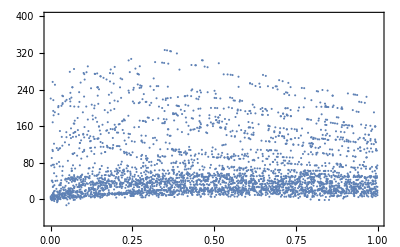

```mathematica
Clear[listn, listnInt, listnIntDP];
listn[gal_] := {1/ rmax[gal]#1, #2} & @@@ gdRBulgeless[{Rad, Vdisk}, gal];
listnInt[gal_, rn_] := Quiet@Interpolation[listn[gal], Method -> "Spline"][rn];
listnIntDP[gal_] :=Table[{rn, listnInt[gal, rn]}, {rn, RandomReal[1, 30]}];
listnIntDPAll =  Flatten[listnIntDP /@ Range[175], 1];
ListPlot[listnIntDPAll, PlotRange->{All, {-50, 400}}, Axes -> False, Frame -> True]
```

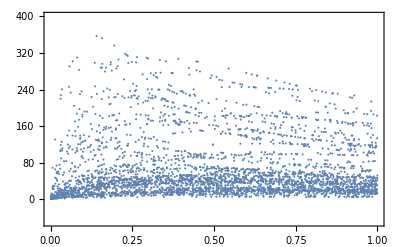

```mathematica
Clear[listCurves, listCurve, rn];
listCurve[gal_] := vExp[rn rmax122[gal], datasetExpVdiskNoBulge[gal, "logSigma0"], datasetExpVdiskNoBulge[gal, "h"]];
listCurveDP[gal_] := Table[{rn, listCurve[gal]}, {rn, RandomReal[1, 30]}]
listCurveDPall = Flatten[listCurveDP /@ Range @ 122, 1];
ListPlot[listCurveDPall, PlotRange->{All, {-50, 400}}, Axes -> False, Frame -> True]
```

## Gas contribution

```mathematica
(*
hGas is the h value for the gas distribution.
hGasn is the hn value for the gas distribution.
frho is the ratio between the gas to stellar central density.
fh is the ratio between hn and hGasn.
*)
```

#### logSigma0gas e hGasn

```mathematica
Clear[associationFitExpVgas];
associationFitExpVgas[galaxyNumber_, dataRVgas_List] := associationFitExpVgas[galaxyNumber, dataRVgas] = Block[
  {galaxyName, luminosity, massHI, sol, R, h, bestLogSigma0, besth, logSigma0, listModel, uncertainty, rMax, solExtended},
  If[
    dataRVgas=={}, 
    Return[{}]
  ];
  galaxyName = galaxy[galaxyNumber];
  luminosity = globalData[[galaxyNumber, colL]];
  massHI = globalData[[galaxyNumber, colMHI]];
  rMax = Last @ dataRVgas[[All, 1]];
  listModel = vExp[# , logSigma0, h] & /@ dataRVgas[[All,1]];
  uncertainty = Max[{0.10 dataRVgas[[#, 2]], 2}] & /@ Range@Length@dataRVgas; (*Max[10%, 2 km/s] uncertainty, inspired on distance error together with a minimum one.*)
  sol = NMinimize[
    {chi2[listModel, dataRVgas[[All, 2]], uncertainty], 100 rMax > h > 0.1, logSigma0 > 0.5},
    {{logSigma0, 3, 10}, {h, 3, 30}},
    Method-> Automatic
  ];
  (*{logSigma0, h, Chi2, Number of data points }*)
  solExtended = {galaxyName, luminosity, massHI, First@sol, First@sol/(Length[dataRVgas] - 2), logSigma0, h, h/rMax, rMax, Length[dataRVgas]} /. Last@sol;
  AssociationThread[{"Name", "L", "MassHI", "Chi2", "Chi2red", "logSigma0Gas", "hGas", "hGasn", "rMax", "dataPoints"}, solExtended]
];
```

```mathematica
Echo["Computing datasetExpVgasNoBulge. This takes some seconds."];
datasetExpVgasNoBulge = Dataset[
  DeleteCases[ 
    associationFitExpVgas[#, gdRBulgeless[{Rad, Vgas}, #]] & /@ Range[175], 
  {}]
] // EchoTiming
```

Computing datasetExpVgasNoBulge. This takes some seconds.

54.1361

```mathematica
Export["headerGasAux.txt", {
  "# Additional velocity distribution: a fast sample analysis for dark matter or modified gravity models",
  "# by A. Hernandez-Arboleda, D. C. Rodrigues, A. Wojnar",
  "# ",
  "# This file: Best fit results of an exponential model for the gaseous component of 122 SPARC galaxies.",
  "# 1st column: galaxy name.",
  "# 2nd column: reference luminosity value from SPARC L (10^9 Msun), not fitted.",
  "# 3rd column: reference HI mass value from SPARC MassHI (10^9 Msun), not fitted.",
  "# 4th column: best-fit disk scale length hGas (kpc).",
  "# 5th column: best-fit central surface density logSigma0Gas (log_10 Msun/kpc^3).",
  "# 6th column: normalized disk scale length hGasn.",
  "# 7th column: the minimum chi-squared value Chi2.",
  "# 8th column: the number of galaxy data points that were used for the fit dataPoints.", 
  "# ",
  "# "
}];

datasetGasExport = datasetExpVgasNoBulge[All,{"Name", "L", "MassHI", "hGas","logSigma0Gas", "hGasn","Chi2", "dataPoints"}];
Export["GasExponentialBestFitAux.tsv", datasetGasExport, Alignment-> Left, "TextDelimiters"->None];

Run["cat headerGasAux.txt GasExponentialBestFitAux.tsv > GasExponentialBestFit.tsv"]; (*It is only guaranteed to work in Unix systems. Sorry Windows...*)

DeleteFile["headerGasAux.txt"];
DeleteFile["GasExponentialBestFitAux.tsv"];

Export["datasetExpVgasNoBulge.m", datasetExpVgasNoBulge];
```

### Testing the approximations

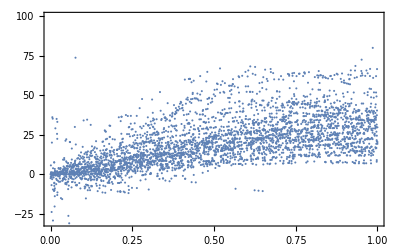

```mathematica
Clear[listn, listnInt, listnIntDP];
listn[gal_] := {1/ rmax[gal]#1, #2} & @@@ gdRBulgeless[{Rad, Vgas}, gal];
listnInt[gal_, rn_] := Quiet@Interpolation[listn[gal], Method -> "Spline"][rn];
listnIntDP[gal_] :=Table[{rn, listnInt[gal, rn]}, {rn, RandomReal[1, 30]}];
listnIntDPAll =  Flatten[listnIntDP /@ Range[175], 1];
ListPlot[listnIntDPAll, PlotRange->{All, {-30, 100}}, Axes -> False, Frame -> True]
```

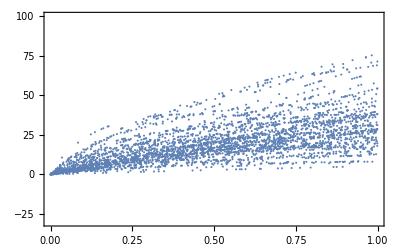

```mathematica
Clear[listCurve, rn, listCurveDP, listCurveDPall];
listCurve[gal_] := vExp[rn rmax122[gal], datasetExpVgasNoBulge[gal, "logSigma0Gas"], datasetExpVgasNoBulge[gal, "hGas"]];
listCurveDP[gal_] := Table[{rn, listCurve[gal]}, {rn, RandomReal[1, 30]}]
listCurveDPall = Flatten[listCurveDP /@ Range @ 122, 1];
ListPlot[listCurveDPall, PlotRange->{All, {-30, 100}}, Axes -> False, Frame -> True]
```

```mathematica
?nSigmaProbability
```

Missing[UnknownSymbol,nSigmaProbability]

```mathematica
$Context
```

Global`

```mathematica
distGas = distributionSilverman @listCurveDPall;
pdfValuenSigmaGas[n_?NumberQ] := FindHDPDFValues[distGas, nSigmaProbability[n]];
(*plotBluePalatini = plotBlue[list2δVVmodelAll, list1LimitsSigmaPalatini, {{xmin, xmax - 0.01}, {-0.5, 2.5}}, PlotRange -> {{0, 0.99}, {-0.5, 2.5}}] *)

Clear[plotPalatiniSigma];
plotPalatiniSigma[n_] := plotPalatiniSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaPalatini[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distPalatini, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];
```